# Script to Generate Regular Patterns for ERACR

## Functions

```mathematica
SetDirectory[NotebookDirectory[]];
PolarToCartesian[r_,θ_]:={r*Cos[θ],r*Sin[θ]}
CartesianToPolar[x_,y_]:={Sqrt[x^2+y^2],ArcTan[y/x]}
FormatForMGDrivE[latLongs_,popSize_]:={#[[1]],#[[2,1]],#[[2,2]],popSize}&/@Transpose[{Range[latLongs//Length],latLongs//N}]
```

## Routine

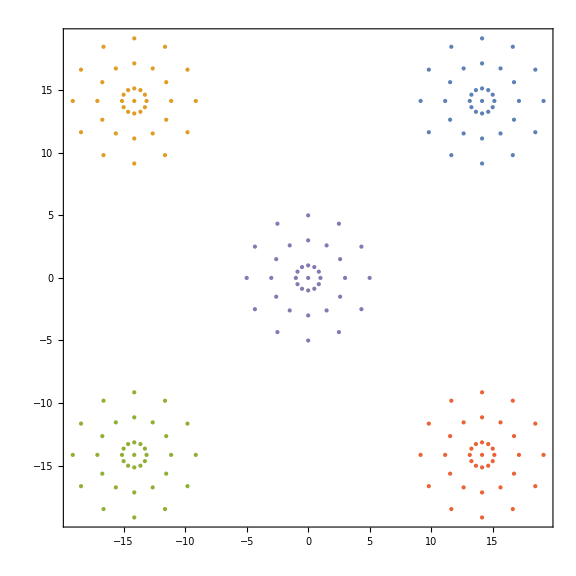

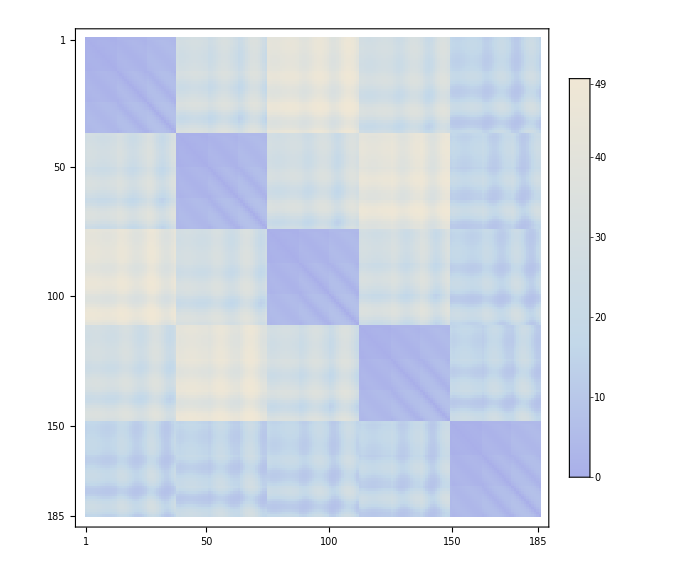

```mathematica
angles=Range[0,2π-π/6,π/6];
radii=Range[1,5,2];
anglesRing=Range[0,2π-π/2,π/2];
{radiusRing,phaseRing}={20,π/4};
noiseLevel=0;
(**)
templatePoints=Table[PolarToCartesian[i,#]&/@angles,{i,radii}];
pointPattern=Prepend[Flatten[templatePoints,1],{0,0}];
(**)
ringCentroids=PolarToCartesian[radiusRing,#]&/@(anglesRing+phaseRing);
fullSet=Flatten[{Table[(i+#)&/@pointPattern,{i,ringCentroids}]//Flatten[#,1]&,pointPattern},1];
fullSetNoisy={#[[1]]+RandomReal[{-noiseLevel,noiseLevel}],#[[2]]+RandomReal[{-noiseLevel,noiseLevel}]}&/@fullSet//N;
clustered=FindClusters[fullSetNoisy];
(**)
listPlot=ListPlot[clustered,
AspectRatio->1,
Frame->True,
FrameStyle->Thick,
Axes->None,
PlotStyle->PointSize[Large],
ImageSize->Large
]
(**)
distances=Table[N[EuclideanDistance[i,#]]&/@fullSetNoisy,{i,fullSetNoisy}];
matrixPlot=MatrixPlot[distances,ColorFunction->"LakeColors",PlotLegends->Automatic,ImageSize->Large]
```

## Export

```mathematica
formattedList=FormatForMGDrivE[fullSet,1000];
Export["FiveCities_Coordinates.csv",formattedList]
Export["FiveCities_Distances.csv",distances]
Export["FiveCities.png",Grid[{{listPlot,matrixPlot}}],ImageSize->2000]
```

FiveCities_Coordinates.csv

FiveCities_Distances.csv

FiveCities.png